# Combined Analysis Ω_DM and Direct Detection limits from lux

```mathematica
SetDirectory["/media/vanniagm/36887AD4887A925B/DataMicros/NuMod/z_2_090915"];
```

List of model parameters

#### Relative Abundance

#### Ω=0.1198+-0.0026

```mathematica
Ωexp = 0.1198; Ωerr = 0.0026; 
vev = 246; 
time1 = SessionTime[];
```

#### Abundance Plot

```mathematica
omf1G=Import["mpsims.1.dat"];Length[omf1G]
```

138

```mathematica
Table[(omf1G[[i,3]]/omf1G[[i,2]])^2,{i,1,Length[omf1G]}]
```

{0.000594693,0.000597213,0.000597896,0.000597896,0.000597896,0.000598299,0.000598299,0.000598299,0.000598738,0.000598738,0.000598738,0.000598866,0.000598866,0.000598866,0.000598958,0.000598958,0.000598958,0.000598958,0.000599026,0.000599026,0.000599026,0.000599026,0.000570176,0.000570176,0.000570176,0.000570176,0.00059919,0.00059919,0.00059919,0.00059919,0.000573432,0.000573432,0.000573432,0.000573432,0.000599024,0.000599024,0.000599024,0.000599024,0.000575772,0.000575772,0.000575772,0.000575772,0.000599108,0.000599108,0.000599108,0.000599108,0.000577906,0.000577906,0.000577906,0.000577906,0.000599801,0.000599801,0.000599801,0.000599801,0.000580299,0.000580299,0.000580299,0.000580299,0.000599626,0.000599626,0.000599626,0.000599626,0.000581596,0.000581596,0.000581596,0.000581596,0.000599476,0.000599476,0.000599476,0.000599476,0.000582711,0.000582711,0.000582711,0.000582711,0.000599346,0.000599346,0.000599346,0.000599346,0.00058368,0.00058368,0.00058368,0.00058368,0.000599233,0.000599233,0.000599233,0.000599233,0.00058453,0.00058453,0.00058453,0.00058453,0.000570362,0.000570362,0.000570362,0.000570362,0.000599714,0.000599714,0.000599714,0.000599714,0.00058585,0.00058585,0.00058585,0.00058585,0.000572461,0.000572461,0.000572461,0.000572461,0.000599593,0.000599593,0.000599593,0.000599593,0.000586489,0.000586489,0.000586489,0.000586489,0.00057381,0.00057381,0.00057381,0.00057381,0.000599484,0.000599484,0.000599484,0.000599484,0.000587062,0.000587062,0.000587062,0.000587062,0.000575021,0.000575021,0.000575021,0.000575021,0.000599387,0.000599387,0.000599387,0.000599387,0.000587578,0.000587578,0.000587578,0.000587578}

```mathematica
Length[omf1G[[1]]]
```

16

```mathematica
om=Import["DATA112415_eqmu.dat"];Length[om]
```

1188

```mathematica
Length[om[[1]]]
```

16

List in order: Mpsi,  Lam,  mu(1), mu(3), Lx, kk, Om, SigmaPsiP, SigmaPsiN, SigTotIncoh, NuFlux from Sun, MuonFlux Upward, MuonFlux Contained, Z width, H width, HBR inv

```mathematica
om[[1188]]
```

{62.,4068.,94.,93.79,0.6,1.,0.12388,7.8272×10^-47,3.2745×10^-47,5.7139×10^-47,2588.2,5.1885×10^-6,0.000046851,2.4098,0.0060502,0.0001023}

```mathematica
ome=Join[omf1G,om];Length[ome]
```

1326

```mathematica
om1=Table[If[ome[[i,1]]≤36,ome[[i]],Unevaluated[Sequence[]]],{i,1,Length[ome]}];Length[om1]
```

316

```mathematica
Max[Table[om1[[i,6]],{i,1,Length[om1]}]]
```

1.333

```mathematica
om2=Table[If[ome[[i,1]]>=36,ome[[i]],Unevaluated[Sequence[]]],{i,1,Length[ome]}];Length[om2]
```

1010

```mathematica
t1=Table[{ome[[i,1]],ome[[i,3]]},{i,1,Length[ome]}];t2=Table[{ome[[i,1]],ome[[i,4]]},{i,1,Length[ome]}];
```

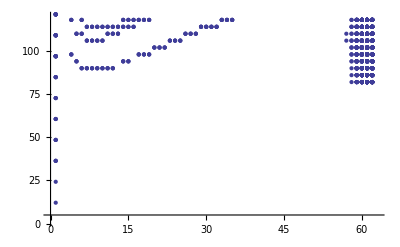

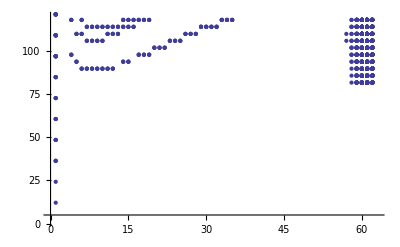

```mathematica
ListPlot[t1,PlotRange->{{0,63},{1,120}}]
ListPlot[t2,PlotRange->{{0,63},{1,120}}]
```

Mdm,Lambda,mu1,mu3,Lx,kk

Effective couplings  
Laeff will be in terms of Psi,Phi,nu coupling which is proportional to zee^tz with our election of e=E delta, with E:Anti-diagonal matrix and mu2=0, z3=1, z2=z1=0, mu1, mu3 free param.

```mathematica
Leff[mpsi_,zd_,kk_,Lam_,mu1_]:=Sqrt[1+((10+mpsi)*kk/mpsi)^2]*Lam*(vev/(Sqrt[2]zd mu1));
```

```mathematica
line1=Line[{{4,1.6},{70,1.6}}];
lineStyle={Thick,Red};
```

```mathematica
MfLeff=Table[{om[[i,1]],Leff[om[[i,1]],2.,om[[i,6]],om[[i,2]],om[[i,3]]]/1000},{i,Length[om]}];
```

```mathematica
Min[Table[MfLeff[[i,2]],{i,1,Length[MfLeff]}]]
```

1.13257

```mathematica
MfLeff1=Table[{om1[[i,1]],Leff[om1[[i,1]],2.,om1[[i,6]],om1[[i,2]],om1[[i,3]]]/1000},{i,Length[om1]}];
```

```mathematica
MfLeff2=Table[{om2[[i,1]],Leff[om2[[i,1]],2.,om2[[i,6]],om2[[i,2]],om2[[i,3]]]/1000},{i,Length[om2]}];
```

```mathematica
omchi=MfLeff;omchi1=MfLeff1;omchi2=MfLeff2;
```

```mathematica
12.623658187416636^2
```

159.357

```mathematica
Export["Leffvsmpsi.pdf",figs1]
```

Leffvsmpsi.pdf

```mathematica
v=246.;
Mpl=1.22093 10^(19);
mw=80.385;
mz=91.1876;
MH=125.0;
GH=.01;
mτ=1.77682;
ΓZ=2.495;
mτ=1.77682;
MTA=mτ;
mh=125.7;
mb=4.66;
MZ=mz;
MB=mb;
cw=mw/mz;
sw=Sqrt[1-cw^2];
gew=2*mw/v;
Gz=2.495;
θ[s_]:=(1+Sign[s])/2;
w=ArcCos[80.385/91.1876];
mt=173.21;
mf=mt;
mudm1=118.;
z3=2;
mudm3=118.;
Lx=0.3;
ciii=Sqrt[2]*z3*mudm1/vev;
cii=2.*((Lam^2/vev^2)z3^2mudm3^2/Lam^2+Lx*z3^2*Log[Lam/mphi]);
cviiL=(Lam^2/vev^2)(z3^2 mudm3^2/Lam^2);
cviiR=(Lam^2/vev^2)(z3^2 mudm3^2/Lam^2)(Log[Lam/mphi]);
BL= (cviiL/ciii^2)(gew/(4 Pi cw))^4 (mfe^2+((10+mfe) )^2)/((mz^2-4 mfe^2)+I mz Gz);
BR= (cviiR/ciii^2)(gew/(4 Pi cw))^4 (mfe^2+((10+mfe) )^2)/((mz^2-4 mfe^2)+I mz Gz);
BB=Abs[BL+BR]/(Abs[BL]^2+Abs[BR]^2);
ResSq=(gew/(4 Pi cw))^4 (mfe^4)/(16 mfe^4+Gz^2 MZ^2-8 mfe^2 MZ^2+MZ^4) ;
ub=(MB/mfe)^2;
uta=(MTA/mfe)^2;
(*sigz=(vev/(Liff*1000))^ 4 (Abs[BL]^2+ Abs[BR]^2)/(2048Sqrt[3]Pi mfe^2);  falta revisar por factor Sqrt[2] que introduje en Leff*)
```

```mathematica
Leff[62,2,1,1000,118.]
```

1129.57

```mathematica
gs[T_]:=2+8*2+3*2*θ[T-mw]+3 θ[T-mz]+θ[T-mh]+(7/8) (2*(4+2+12+12)+4 θ[T-mτ]+2+12 θ[T-mb]+12 θ[T-mt]);
g=4;(*dirac fermion*)(*relic abundance*)(* <σ v>:*)

(*Lam=1000 Liff*z3*mudm1 Sqrt[2]/(Sqrt[1+(Mscalar^2/mfe^2)]vev);*)
```

```mathematica
σ1[mph_,lamb_]:=(vev/(1000*Liff))^4/(256 mfe^2 Pi) (1+ResSq(1+mph^2/mfe^2)^2(1+Log[lamb/mph])^2);
σ2=(3 (cii^2 MB^2 (mfe^2-MB^2)^(3/2) ))/(1024 (Lam^2 mfe π^5 ((MH^2-4 mfe^2)^2+MH^2 GH^2)));σzb=sigz*(9/4 (1+4BB)-3/2 ub(BB-1)+(1+4BB+2ub BB)sw^2(2sw^2-3));
σzta=sigz*12( (1+4BB)-2 uta(BB-1)+4(1+4BB+2uta BB)sw^2(2sw^2-1));
σ0[msca_,lan_]:=σ1[msca,lan];(*σzb+σzta;*)

xf[msd_,lamn_]:=Log[0.038 (g/Sqrt[gs[mfe]]) Mpl mfe σ0[msd,lamn]]-(1/2) Log[Log[0.038 (g/Sqrt[gs[mfe]]) Mpl mfe σ0[msd,lamn]]];
Ω[msd_,lamn_]:=1.07 10^9 xf[msd,lamn]/(Sqrt[gs[mfe]] Mpl σ0[msd,lamn]);
```

```mathematica
256/64
```

4

```mathematica
Ω[85,1000]/.mfe->45/.Liff->.9
```

0.0554039

v^2/(2*z3^2 Leff^2)(1+ms^2/mfe^2)< delta^2

```mathematica
RegZinv[mphi_]:=vev^2/(8(Liff*1000)^2)(1+mphi^2/mfe^2)
```

{{1.,5.04751},{4.,3.23052},{5.,2.92592},{6.,2.71347},{7.,2.5381},{8.,2.37943},{9.,2.25744},{10.,2.16089},{11.,2.05334},{12.,1.98968},{13.,1.93628},{14.,1.82454},{15.,1.78686},{16.,1.75412},{17.,1.66567},{18.,1.6412},{19.,1.61943},{20.,1.5372},{21.,1.52035},{22.,1.50511},{23.,1.43498},{24.,1.42281},{25.,1.41166},{26.,1.35045},{27.,1.34133},{28.,1.3329},{29.,1.27858},{30.,1.27155},{31.,1.265},{32.,1.25887},{33.,1.21065},{34.,1.20545},{35.,1.20055}}

{{1.,5.17698},{4.,3.23298},{5.,3.0129},{6.,2.75225},{7.,2.59676},{8.,2.43443},{9.,2.30962},{10.,2.21083},{11.,2.08604},{12.,2.01812},{13.,1.95435},{14.,1.83852},{15.,1.79838},{16.,1.75851},{17.,1.66694},{18.,1.64245},{19.,1.62067},{20.,1.5372},{21.,1.52035},{22.,1.50511},{23.,1.43498},{24.,1.42281},{25.,1.41166},{26.,1.35045},{27.,1.34133},{28.,1.3329},{29.,1.27858},{30.,1.27155},{31.,1.265},{32.,1.25887},{33.,1.21065},{34.,1.20545},{35.,1.20055}}

InterpolatingFunction::dmval: Input value {0.000715} lies outside the range of data in the interpolating function. Extrapolation will be used.

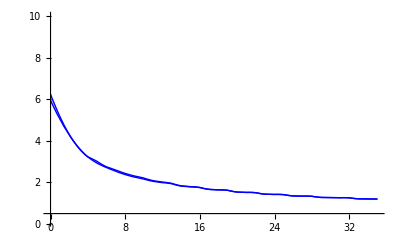

```mathematica
Lb1=(First[SortBy[#1,Last]]&)/@SplitBy[omchi1[[All,{1,2}]],First]
Lb2=(Last[SortBy[#1,Last]]&)/@SplitBy[omchi1[[All,{1,2}]],First]
Fb1=Interpolation[Lb1[[All,{1,2}]],InterpolationOrder->2];
Fb2=Interpolation[Lb2[[All,{1,2}]],InterpolationOrder->2];
figs1=Show[Plot[{Fb1[m],Fb2[m]},{m,0,35},PlotRange->{.1,10},PlotStyle->{Blue,Blue},Filling->{1->{2}}]]
```

{{57.,1.22022},{58.,1.60033},{59.,1.36512},{60.,1.13257},{61.,1.71089},{62.,1.9587}}

{{57.,1.26626},{58.,2.22026},{59.,4.1863},{60.,7.52123},{61.,11.2481},{62.,10.3325}}

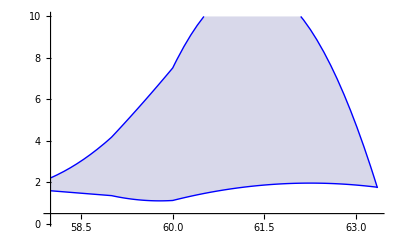

```mathematica
lo2=(First[SortBy[#1,Last]]&)/@SplitBy[omchi2[[All,{1,2}]],First]
lo22=(Last[SortBy[#1,Last]]&)/@SplitBy[omchi2[[All,{1,2}]],First]
fi2=Interpolation[lo2[[All,{1,2}]],InterpolationOrder->2];
fi22=Interpolation[lo22[[All,{1,2}]],InterpolationOrder->2];
figs1=Show[Plot[{fi2[m],fi22[m]},{m,58,63.35},PlotRange->{.1,10},PlotStyle->{Blue,Blue},Filling->{1->{2}}]]
```

```mathematica
Higgs constraints
```

constraints Higgs

```mathematica
Lamm[mu3_,zz3_,mps_,Laff_]:=1000 Laff*zz3*mu3 Sqrt[2]/(Sqrt[1+((10+mps))^2/mps^2]vev);
```

```mathematica
RegHinv[lxx_,lamm_,mss_]:=(vev/(lamm))*((.014)*4*lamm^2/vev^2+lxx 4 Log[lamm/mss]);
```

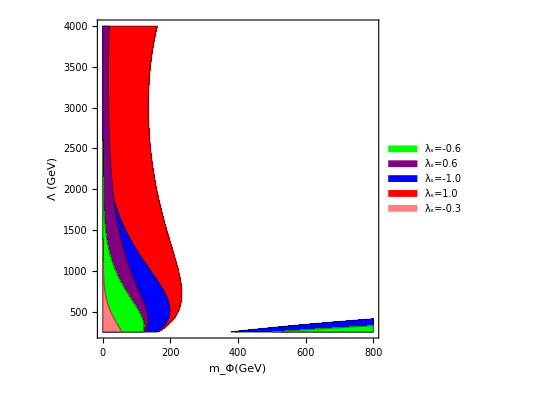

```mathematica
regH=Show[RegionPlot[Abs[RegHinv[1,la,mss]]>1.7,{mss,.1,800},{la,250,4000},PlotStyle->Red,PlotLegends->Placed[SwatchLegend[{Red},{"λ_x=1.0"},LabelStyle->16],{0.52,.85}]],RegionPlot[Abs[RegHinv[-1,la,mss]]>1.7,{mss,.1,800},{la,250,4000},PlotStyle->Blue,PlotLegends->Placed[SwatchLegend[{Blue},{"λ_x=-1.0"},LabelStyle->16],{0.52,.75}]],RegionPlot[Abs[RegHinv[.6,la,mss]]>1.7,{mss,.1,800},{la,250,4000},PlotStyle->Purple,PlotLegends->Placed[SwatchLegend[{Purple},{"λ_x=0.6"},LabelStyle->16],{0.52,.65}]],RegionPlot[Abs[RegHinv[-.6,la,mss]]>1.7,{mss,.1,800},{la,250,4000},PlotStyle->Green,PlotLegends->Placed[SwatchLegend[{Green},{"λ_x=-0.6"},LabelStyle->16],{0.52,.55}]],RegionPlot[Abs[RegHinv[-.3,la,mss]]>1.7,{mss,.1,800},{la,250,4000},PlotStyle->Pink,PlotLegends->Placed[SwatchLegend[{Pink},{"λ_x=-0.3"},LabelStyle->16],{0.52,.45}]],Frame->True,FrameLabel->{"m_Φ(GeV)","Λ (GeV)"},LabelStyle->{(*FontWeight->"Bold"*)FontSize->20}(*ListLogLogPlot[t3,PlotRange->{{1,200},{0,2*10^10}},PlotStyle->{Blue}]*),PlotRangePadding->0,ImageSize->{GoldenRatio*400,400}]
```

```mathematica
Export["RegHinv.pdf",regH]
```

RegHinv.pdf

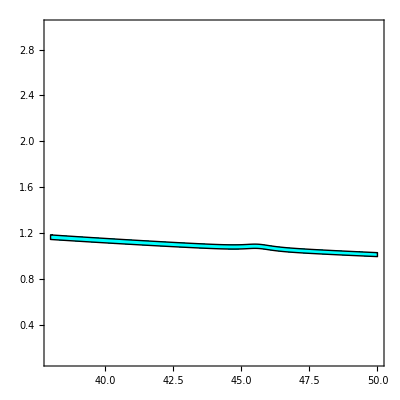

```mathematica
RegionPlot[0.1198-3 0.0026<Ω[(10+mfe)*1,1000]<0.1198+3 0.0026,{mfe,38,50},{Liff,.1,3},PlotPoints->100,PlotStyle->Cyan,BoundaryStyle->Directive[ Thin]]
```

InterpolatingFunction::dmval: Input value {56.7001} lies outside the range of data in the interpolating function. Extrapolation will be used.

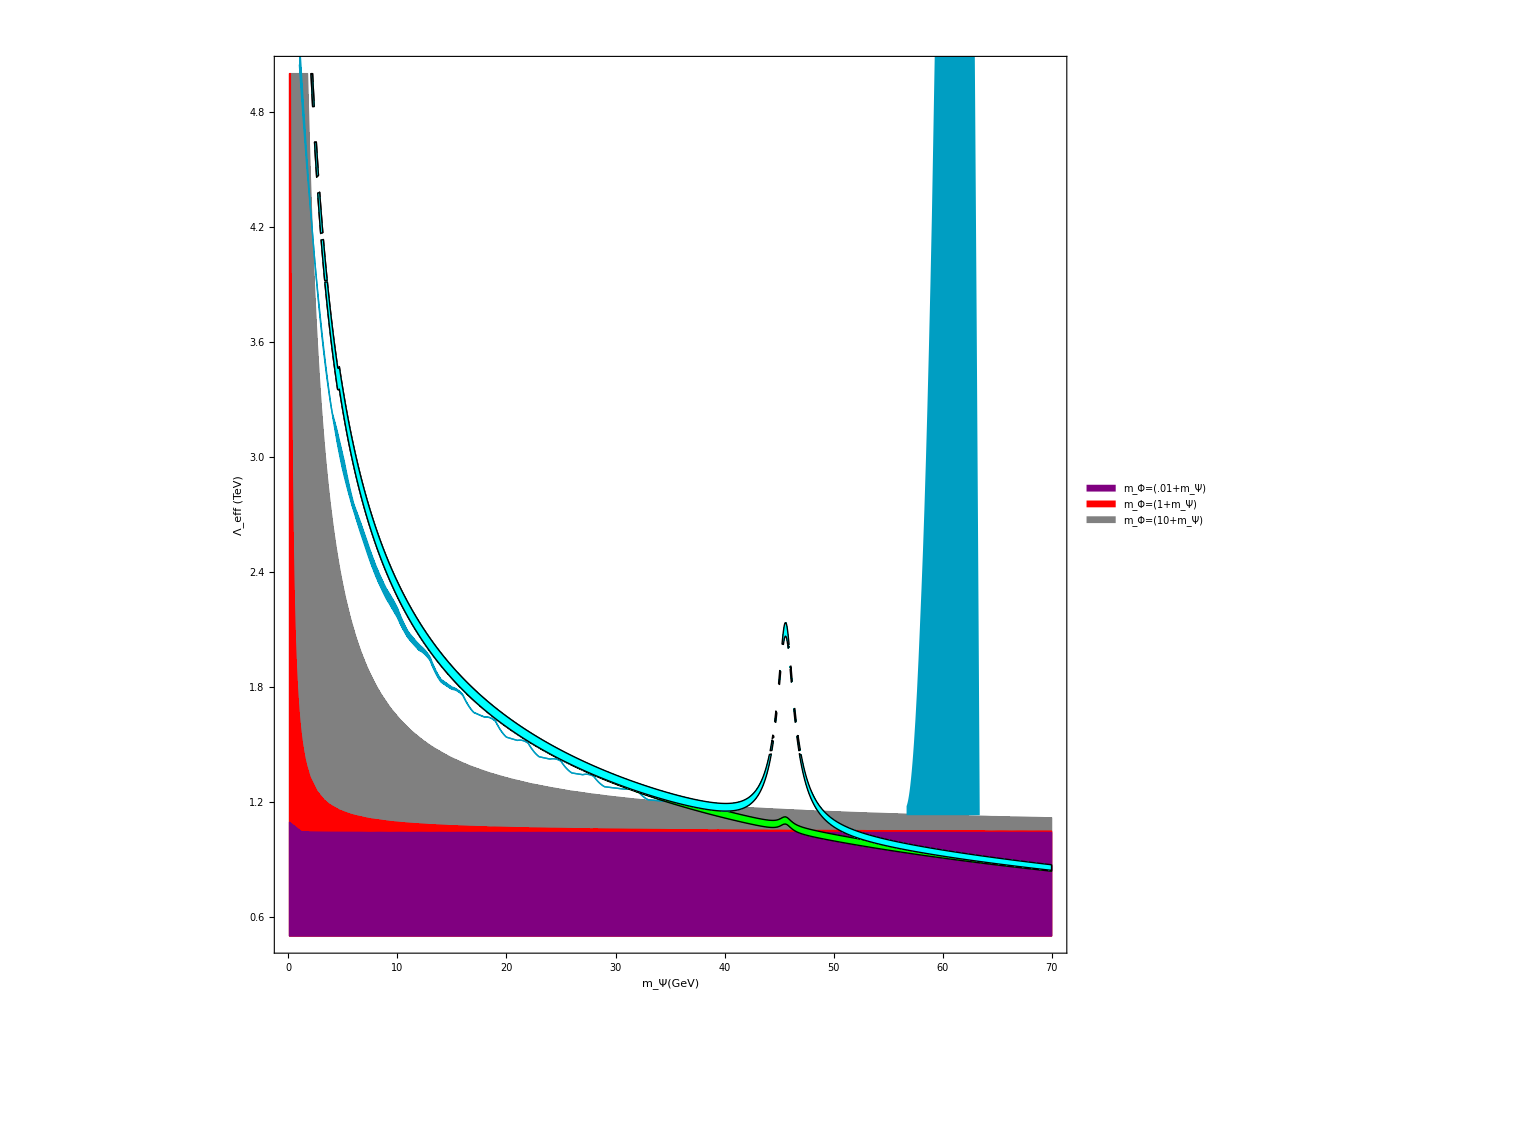

```mathematica
fig4=Show[
RegionPlot[RegZinv[(mfe+10)*1]>.014,{mfe,.1,70},{Liff,.5,5},PlotStyle->Gray,BoundaryStyle->Directive[Gray, Thin],PlotLegends->Placed[SwatchLegend[{Gray},{"m_Φ=(10+m_Ψ)"},LabelStyle->16],{0.52,.55}]],
RegionPlot[RegZinv[(mfe+1)*1]>.014,{mfe,.1,70},{Liff,.5,5},PlotStyle->Red,BoundaryStyle->Directive[Red, Thin],PlotLegends->Placed[SwatchLegend[{Red},{"m_Φ=(1+m_Ψ)"},LabelStyle->16],{0.52,.45}]],
RegionPlot[RegZinv[(mfe+.01)*1]>.014,{mfe,.1,70},{Liff,.5,5},PlotStyle->Purple,BoundaryStyle->Directive[Purple, Thin],PlotLegends->Placed[SwatchLegend[{Purple},{"m_Φ=(.01+m_Ψ)"},LabelStyle->16],{0.52,.35}]],
Plot[{Fb1[m],Fb2[m]},{m,1,35},PlotRange->{.1,10},PlotStyle->{RGBColor[0,0.62,0.76],RGBColor[0,0.62,0.76]},Filling->{1->{2}},FillingStyle->RGBColor[0,0.62,0.76]],(*ListPlot[{omchi1},PlotRange->{{1,70},{.1,10}},PlotStyle->PointSize[.002]],ListPlot[{omchi2},PlotStyle->PointSize[.002]],*)
RegionPlot[0.1198-3 0.0026<Ω[(mfe+.1),10000]<0.1198+3 0.0026,{mfe,.1,70},{Liff,.1,5},PlotPoints->200,PlotStyle->Green,BoundaryStyle->Directive[ Thin]],
RegionPlot[0.1198-3 0.0026<Ω[(mfe+10)*4,10000]<0.1198+3 0.0026,{mfe,.1,70},{Liff,.1,5},PlotPoints->200,PlotStyle->Cyan,BoundaryStyle->Directive[ Thin]],
Plot[{1.13,fi22[m]},{m,56.7,63.41},PlotRange->{.1,10},PlotStyle->{None,None},Filling->{2->{1}},FillingStyle->RGBColor[0,0.62,0.76]],
Frame->True,FrameLabel->{"m_Ψ(GeV)","Λ_eff (TeV)"},LabelStyle->{(*FontWeight->"Bold"*)FontSize->20}(*ListLogLogPlot[t3,PlotRange->{{1,200},{0,2*10^10}},PlotStyle->{Blue}]*),PlotRangePadding->0,ImageSize->{GoldenRatio*400,400}]
```

```mathematica
Export["Leffvsmpsi3.pdf",fig4]
```

Leffvsmpsi3.pdf

Minimum Leff ~1.6 TeV

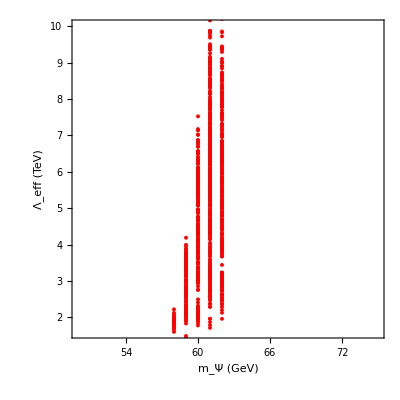

```mathematica
fig5=Show[RegionPlot[0.1198-3 0.0026<Ω<0.1198+3 0.0026,{mfe,50,75},{Liff,1.6,10},PlotPoints->150,FrameLabel->{"\!\(\*SubscriptBox[\(m\), \(Ψ\)]\)     (GeV)","\!\(\*SubscriptBox[\(Λ\), \(eff\)]\) (TeV)","",""},LabelStyle->Large](*,ListPlot[{omchi},PlotRange->{{1,100},{.1,10}}]*),ListPlot[{omchi2},PlotStyle->Red],ImageSize->{GoldenRatio*500,500}]
```

```mathematica
Export["Leffvsmpsi3.png",fig4]
```

Leffvsmpsi3.png

```mathematica
RegZinv[mphi_]:=vev^2/(8*(Liff*1000)^2)(1+mphi^2/mfe^2)
```

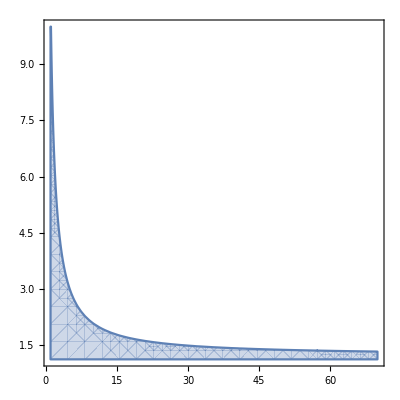

```mathematica
RegionPlot[RegZinv[(mfe+10)*1.33]>.014,{mfe,1,70},{Liff,1.13,10}]
```

Direct Detection

```mathematica
Get["/home/vanniagm/Dropbox/nu_portal/MATH_NUMODEL/atlas15_lux14_xenon1T_lux15.m"]
```

InterpolatingFunction::dmval: Input value {605.825} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {546.712} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {645.448} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

/home/vanniagm/Dropbox/nu_portal

```mathematica
clxms1=Table[If[om1[[i,6]]<1,{om1[[i,1]],om1[[i,10]]},Unevaluated[Sequence[]]],{i,1,Length[om1]}];
clxms2=Table[If[om1[[i,6]]>1,{om1[[i,1]],om1[[i,10]]},Unevaluated[Sequence[]]],{i,1,Length[om1]}];
```

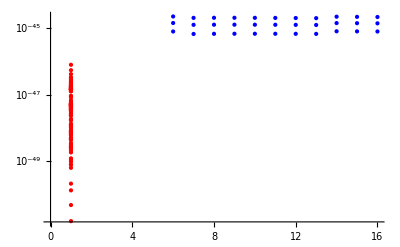

```mathematica
ListLogPlot[{clxms1,clxms2},PlotStyle->{Red,Blue}]
```

```mathematica
clxlx1=Table[If[om1[[i,5]]>0,{om1[[i,1]],om1[[i,10]]},Unevaluated[Sequence[]]],{i,1,Length[om1]}];
clxlx2=Table[If[om1[[i,5]]<0,{om1[[i,1]],om1[[i,10]]},Unevaluated[Sequence[]]],{i,1,Length[om1]}];
```

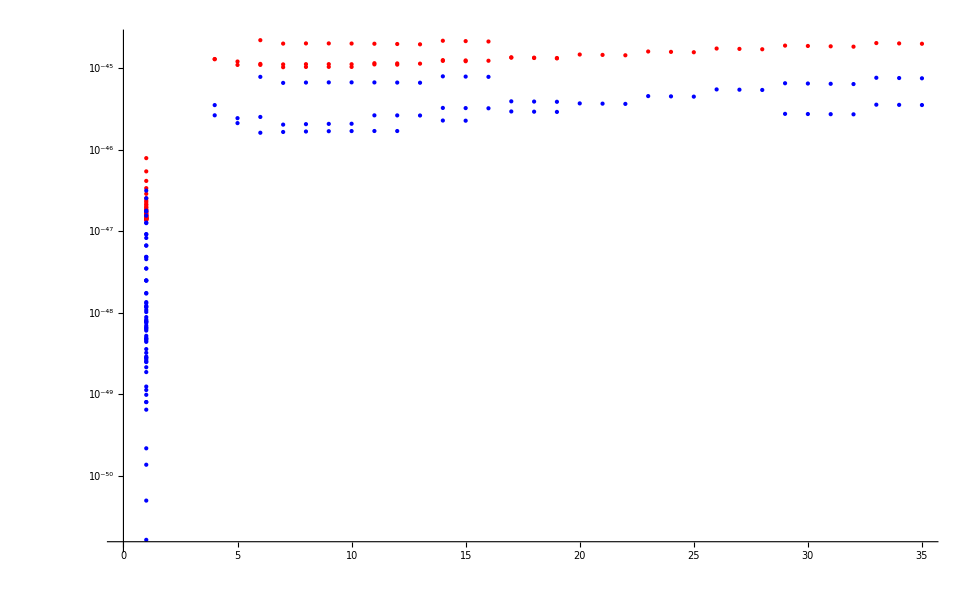

```mathematica
ListLogPlot[{clxlx1,clxlx2},PlotStyle->{Red,Blue}]
```

```mathematica
clxla1=Table[If[om1[[i,2]]>1000,{om1[[i,1]],om1[[i,10]]},Unevaluated[Sequence[]]],{i,1,Length[om1]}];
clxla2=Table[If[om1[[i,2]]<1000,{om1[[i,1]],om1[[i,10]]},Unevaluated[Sequence[]]],{i,1,Length[om1]}];
```

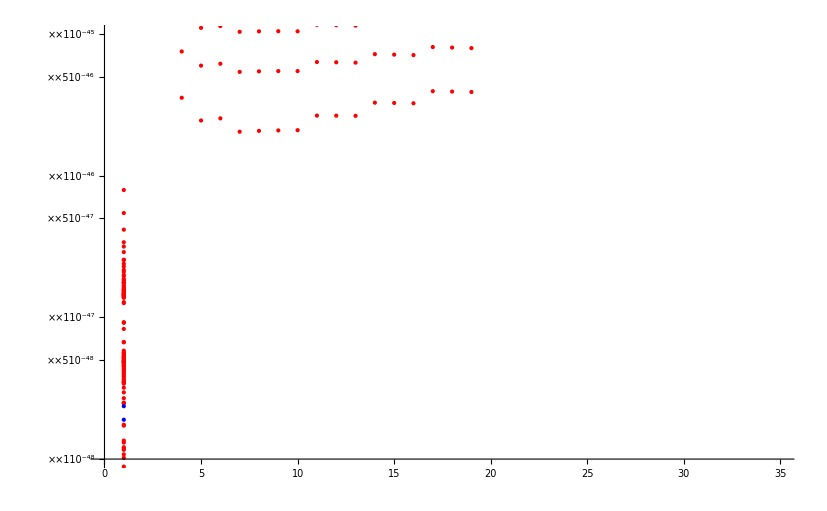

```mathematica
ListLogPlot[{clxla1,clxla2},PlotStyle->{Red,Blue},PlotRange->{{0,35},{10^-48,10^-45}}]
```

```mathematica
Sqrt[.014]
```

0.118322

```mathematica
sigeta=Table[If[om1[[i,6]]<1&&om1[[i,5]]==-.6,{(om1[[i,3]]/om1[[i,2]])^2,om1[[i,10]]},Unevaluated[Sequence[]]],{i,1,Length[om1]}];
sigeta2=Table[If[om1[[i,6]]<1&&om1[[i,5]]==-.3&&om1[[i,2]]<6400,{(om1[[i,3]]/om1[[i,2]])^2,om1[[i,10]]},Unevaluated[Sequence[]]],{i,1,Length[om1]}]
sigeta22=Table[If[om1[[i,6]]<1&&om1[[i,5]]==-.3&&om1[[i,2]]>6400,{(om1[[i,3]]/om1[[i,2]])^2,om1[[i,10]]},Unevaluated[Sequence[]]],{i,1,Length[om1]}]
sigeta3=Table[If[om1[[i,6]]<1&&om1[[i,5]]==0.,{(om1[[i,3]]/om1[[i,2]])^2,om1[[i,10]]},Unevaluated[Sequence[]]],{i,1,Length[om1]}];
sigeta4=Table[If[om1[[i,6]]<1&&om1[[i,5]]==.3,{(om1[[i,3]]/om1[[i,2]])^2,om1[[i,10]]},Unevaluated[Sequence[]]],{i,1,Length[om1]}]
```

{{0.000597896,3.1622×10^-47},{0.000598299,1.556×10^-47},{0.000598738,8.2888×10^-48},{0.000598866,4.5527×10^-48},{0.000598958,2.4894×10^-48},{0.000599026,1.3079×10^-48},{0.000570176,1.3504×10^-48},{0.00059919,6.2835×10^-49},{0.000573432,6.6653×10^-49},{0.000599024,2.5125×10^-49},{0.000575772,2.7897×10^-49},{0.000599108,6.4483×10^-50},{0.000577906,7.9953×10^-50},{0.000599801,1.6238×10^-51},{0.000580299,4.9279×10^-51}}

{{0.000599626,2.1615×10^-50},{0.000581596,1.3589×10^-50},{0.000599476,9.8183×10^-50},{0.000582711,7.9923×10^-50},{0.000599346,2.1403×10^-49},{0.00058368,1.8667×10^-49},{0.000599233,3.5751×10^-49},{0.00058453,3.2209×10^-49},{0.000570362,2.8986×10^-49},{0.000599714,5.2058×10^-49},{0.00058585,4.7809×10^-49},{0.000572461,4.389×10^-49},{0.000599593,6.9766×10^-49},{0.000586489,6.4893×10^-49},{0.00057381,6.0359×10^-49},{0.000599484,8.8476×10^-49},{0.000587062,8.3055×10^-49},{0.000575021,7.7975×10^-49},{0.000599387,1.079×10^-48},{0.000587578,1.02×10^-48}}

{{0.000597896,7.9252×10^-47},{0.000598299,5.4504×10^-47},{0.000598738,4.1617×10^-47},{0.000598866,3.3919×10^-47},{0.000598958,2.8894×10^-47},{0.000599026,2.5407×10^-47},{0.000570176,2.3906×10^-47},{0.00059919,2.2876×10^-47},{0.000573432,2.1644×10^-47},{0.000599024,2.0976×10^-47},{0.000575772,1.9937×10^-47},{0.000599108,1.9513×10^-47},{0.000577906,1.8617×10^-47},{0.000599801,1.8363×10^-47},{0.000580299,1.7577×10^-47},{0.000599626,1.7444×10^-47},{0.000581596,1.6745×10^-47},{0.000599476,1.6703×10^-47},{0.000582711,1.6073×10^-47},{0.000599346,1.6098×10^-47},{0.00058368,1.5524×10^-47},{0.000599233,1.5601×10^-47},{0.00058453,1.5075×10^-47},{0.000570362,1.4573×10^-47},{0.000599714,1.5191×10^-47},{0.00058585,1.4705×10^-47},{0.000572461,1.424×10^-47},{0.000599593,1.4853×10^-47},{0.000586489,1.44×10^-47},{0.00057381,1.3966×10^-47},{0.000599484,1.4573×10^-47},{0.000587062,1.4149×10^-47},{0.000575021,1.3742×10^-47},{0.000599387,1.4342×10^-47},{0.000587578,1.3943×10^-47}}

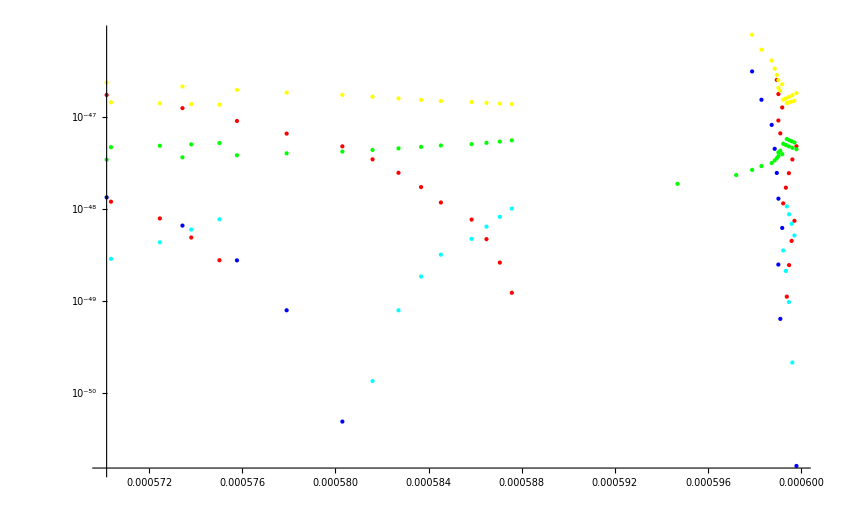

```mathematica
sigetafig=ListLogPlot[{sigeta,sigeta2,sigeta22,sigeta3,sigeta4},PlotStyle->{Red,Blue,Cyan,Green,Yellow}]
```

```mathematica
Export["DD_mudep.pdf",sigetafig]
```

DD_mudep.pdf

```mathematica
Zsig[mmu_,lam_]:=(mu/lam)^2*4(1+Log[lam/1.01])
```

```mathematica
Hsig[mmu_,lam_,lx_]:=2*(246/lam)((mu/lam)^2*4*lam^2/246^2+lx 4 Log[lam/1.01])
```

```mathematica
230.3,1.4149
```

```mathematica
Hsig[145.5,6040,-.3]
Hsig[145.5,6040,.3]
```

-0.844007

0.856074

```mathematica
Zsig[145.5,6040]
```

0.00119135

```mathematica
Hsig[36.36,1487,-.3]
```

-2.87173

```mathematica
Zsig[157.6,6436]
```

0.00105613

```mathematica
clx6=Table[If[om1[[i,5]]<=-.3&&om1[[i,6]]==1&&om1[[i,2]]==1000,{om1[[i,1]],om1[[i,10]]},Unevaluated[Sequence[]]],{i,1,Length[om1]}]
```

{{4.,2.6606×10^-46},{5.,2.1336×10^-46},{6.,1.6248×10^-46},{7.,1.6609×10^-46},{8.,1.6836×10^-46},{9.,1.6972×10^-46},{10.,1.7043×10^-46},{11.,1.7069×10^-46},{12.,1.7062×10^-46},{14.,2.2954×10^-46},{15.,2.2854×10^-46},{17.,2.9669×10^-46},{18.,2.9486×10^-46},{19.,2.9297×10^-46},{20.,3.727×10^-46},{21.,3.7008×10^-46},{22.,3.6744×10^-46},{23.,4.5808×10^-46},{24.,4.5467×10^-46},{25.,4.5129×10^-46},{26.,5.5333×10^-46},{27.,5.4912×10^-46},{28.,5.4497×10^-46},{29.,2.7719×10^-46},{29.,6.5892×10^-46},{30.,2.7596×10^-46},{30.,6.539×10^-46},{31.,2.7474×10^-46},{31.,6.4896×10^-46},{32.,2.7352×10^-46},{32.,6.4409×10^-46},{33.,3.5937×10^-46},{33.,7.6947×10^-46},{34.,3.5759×10^-46},{34.,7.6371×10^-46},{35.,3.5583×10^-46},{35.,7.5805×10^-46}}

```mathematica
clx6II={{4.,2.6606*^-46},{5.,2.1336*^-46},{12.,1.7062*^-46},{19.,2.9297*^-46},{22.,3.6744*^-46},{25.,4.5129*^-46},{32.,2.7352*^-46},{35.,3.5583*^-46}}
```

{{4.,2.6606×10^-46},{5.,2.1336×10^-46},{12.,1.7062×10^-46},{19.,2.9297×10^-46},{22.,3.6744×10^-46},{25.,4.5129×10^-46},{32.,2.7352×10^-46},{35.,3.5583×10^-46}}

```mathematica
Export["LimInfDD.dat",clx6II]
```

LimInfDD.dat

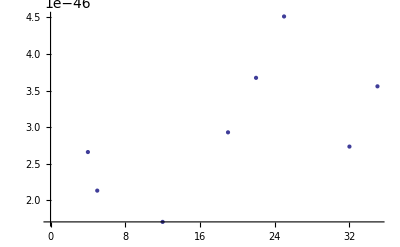

```mathematica
ListPlot[clx6II]
```

```mathematica
clx=Interpolation[clx6II,InterpolationOrder->5]
```

InterpolatingFunction[{{4.,35.}},<>]

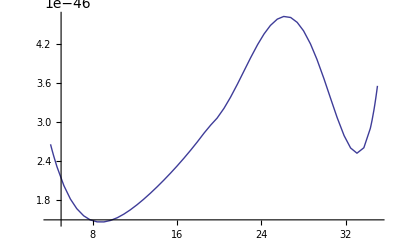

```mathematica
Plot[clx[mfe],{mfe,4,35}]
```

```mathematica
sigmpsinoncoh=Table[{om1[[i,1]],om1[[i,10]]},{i,1,Length[om1]}]
sigmpsinoncoh2=Table[{om2[[i,1]],om2[[i,10]]},{i,1,Length[om2]}];
```

{{4.,2.6606×10^-46},{4.,6.8829×10^-46},{4.,1.3075×10^-45},{4.,3.5519×10^-46},{4.,7.5319×10^-46},{4.,1.299×10^-45},{5.,2.1336×10^-46},{5.,6.1287×10^-46},{5.,1.2184×10^-45},{5.,2.454×10^-46},{5.,5.9851×10^-46},{5.,1.1065×10^-45},{6.,1.6248×10^-46},{6.,5.2948×10^-46},{6.,1.1072×10^-45},{6.,7.8945×10^-46},{6.,1.4173×10^-45},{6.,2.2275×10^-45},{6.,2.5401×10^-46},{6.,6.1712×10^-46},{6.,1.1388×10^-45},{7.,1.6609×10^-46},{7.,5.3826×10^-46},{7.,1.1231×10^-45},{7.,6.6559×10^-46},{7.,1.252×10^-45},{7.,2.0221×10^-45},{7.,2.0451×10^-46},{7.,5.4072×10^-46},{7.,1.0372×10^-45},{8.,1.6836×10^-46},{8.,5.4271×10^-46},{8.,1.1301×10^-45},{8.,6.7216×10^-46},{8.,1.2608×10^-45},{8.,2.033×10^-45},{8.,2.0722×10^-46},{8.,5.457×10^-46},{8.,1.0449×10^-45},{9.,1.6972×10^-46},{9.,5.4427×10^-46},{9.,1.1311×10^-45},{9.,6.7513×10^-46},{9.,1.2629×10^-45},{9.,2.0333×10^-45},{9.,2.0881×10^-46},{9.,5.4776×10^-46},{9.,1.0471×10^-45},{10.,1.7043×10^-46},{10.,5.4386×10^-46},{10.,1.128×10^-45},{10.,6.7562×10^-46},{10.,1.2605×10^-45},{10.,2.0263×10^-45},{10.,2.096×10^-46},{10.,5.4782×10^-46},{10.,1.0454×10^-45},{11.,1.7069×10^-46},{11.,5.4207×10^-46},{11.,1.1222×10^-45},{11.,6.7437×10^-46},{11.,1.2549×10^-45},{11.,2.0144×10^-45},{11.,2.6573×10^-46},{11.,6.3464×10^-46},{11.,1.1616×10^-45},{12.,1.7062×10^-46},{12.,5.3931×10^-46},{12.,1.1145×10^-45},{12.,6.7187×10^-46},{12.,1.2472×10^-45},{12.,1.999×10^-45},{12.,2.6541×10^-46},{12.,6.3192×10^-46},{12.,1.155×10^-45},{13.,6.6849×10^-46},{13.,1.2379×10^-45},{13.,1.9814×10^-45},{13.,2.6472×10^-46},{13.,6.2839×10^-46},{13.,1.1469×10^-45},{14.,2.2954×10^-46},{14.,6.3423×10^-46},{14.,1.2402×10^-45},{14.,8.0101×10^-46},{14.,1.4109×10^-45},{14.,2.1922×10^-45},{14.,3.279×10^-46},{14.,7.2109×10^-46},{14.,1.2672×10^-45},{15.,2.2854×10^-46},{15.,6.2915×10^-46},{15.,1.2284×10^-45},{15.,7.9545×10^-46},{15.,1.3982×10^-45},{15.,2.1697×10^-45},{15.,3.2635×10^-46},{15.,7.1585×10^-46},{15.,1.2564×10^-45},{16.,7.8952×10^-46},{16.,1.3849×10^-45},{16.,2.1464×10^-45},{16.,3.2461×10^-46},{16.,7.1029×10^-46},{16.,1.2451×10^-45},{17.,2.9669×10^-46},{17.,7.317×10^-46},{17.,1.3598×10^-45},{17.,3.9512×10^-46},{17.,8.0968×10^-46},{17.,1.3714×10^-45},{18.,2.9486×10^-46},{18.,7.2503×10^-46},{18.,1.3455×10^-45},{18.,3.9262×10^-46},{18.,8.0285×10^-46},{18.,1.3583×10^-45},{19.,2.9297×10^-46},{19.,7.1828×10^-46},{19.,1.3312×10^-45},{19.,3.9005×10^-46},{19.,7.9593×10^-46},{19.,1.345×10^-45},{20.,3.727×10^-46},{20.,8.3635×10^-46},{20.,1.4849×10^-45},{21.,3.7008×10^-46},{21.,8.2841×10^-46},{21.,1.469×10^-45},{22.,3.6744×10^-46},{22.,8.2052×10^-46},{22.,1.4532×10^-45},{23.,4.5808×10^-46},{23.,9.4931×10^-46},{23.,1.6176×10^-45},{24.,4.5467×10^-46},{24.,9.4028×10^-46},{24.,1.6004×10^-45},{25.,4.5129×10^-46},{25.,9.3137×10^-46},{25.,1.5835×10^-45},{26.,5.5333×10^-46},{26.,1.0714×10^-45},{26.,1.7592×10^-45},{27.,5.4912×10^-46},{27.,1.0614×10^-45},{27.,1.7409×10^-45},{28.,5.4497×10^-46},{28.,1.0515×10^-45},{28.,1.7231×10^-45},{29.,2.7719×10^-46},{29.,6.5892×10^-46},{29.,1.2034×10^-45},{29.,1.9106×10^-45},{30.,2.7596×10^-46},{30.,6.539×10^-46},{30.,1.1924×10^-45},{30.,1.8914×10^-45},{31.,2.7474×10^-46},{31.,6.4896×10^-46},{31.,1.1816×10^-45},{31.,1.8726×10^-45},{32.,2.7352×10^-46},{32.,6.4409×10^-46},{32.,1.171×10^-45},{32.,1.8541×10^-45},{33.,3.5937×10^-46},{33.,7.6947×10^-46},{33.,1.3338×10^-45},{33.,2.0525×10^-45},{34.,3.5759×10^-46},{34.,7.6371×10^-46},{34.,1.3221×10^-45},{34.,2.0327×10^-45},{35.,3.5583×10^-46},{35.,7.5805×10^-46},{35.,1.3106×10^-45},{35.,2.0134×10^-45}}

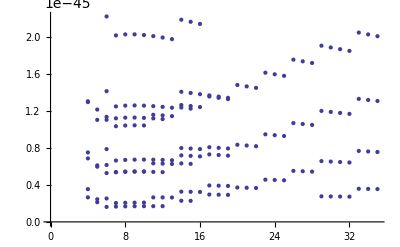

```mathematica
ListPlot[sigmpsinoncoh]
```

```mathematica
sigmpsinoncoh3=Table[{om1[[i,1]],om1[[i,2]],om1[[i,10]]*10^45},{i,1,Length[om1]}];
```

```mathematica
sigmpsi2coh=Table[{om[[i,1]],(om[[i,8]]+om[[i,9]])/2},{i,1,Length[om]}];
siglx=Table[{om[[i,5]],om[[i,10]]},{i,1,Length[om]}];
siglam=Table[{om[[i,2]],om[[i,10]]},{i,1,Length[om]}];
```

```mathematica
Lb1=(First[SortBy[#1,Last]]&)/@SplitBy[sigmpsinoncoh[[All,{1,2}]],First];
Lb2=(Last[SortBy[#1,Last]]&)/@SplitBy[sigmpsinoncoh[[All,{1,2}]],First]
Fb1=Interpolation[Lb1[[All,{1,2}]],InterpolationOrder->2];
Fb2=Interpolation[Lb2[[All,{1,2}]],InterpolationOrder->2]
```

{{4.,1.3075×10^-45},{5.,1.2184×10^-45},{6.,2.2275×10^-45},{7.,2.0221×10^-45},{8.,2.033×10^-45},{9.,2.0333×10^-45},{10.,2.0263×10^-45},{11.,2.0144×10^-45},{12.,1.999×10^-45},{13.,1.9814×10^-45},{14.,2.1922×10^-45},{15.,2.1697×10^-45},{16.,2.1464×10^-45},{17.,1.3714×10^-45},{18.,1.3583×10^-45},{19.,1.345×10^-45},{20.,1.4849×10^-45},{21.,1.469×10^-45},{22.,1.4532×10^-45},{23.,1.6176×10^-45},{24.,1.6004×10^-45},{25.,1.5835×10^-45},{26.,1.7592×10^-45},{27.,1.7409×10^-45},{28.,1.7231×10^-45},{29.,1.9106×10^-45},{30.,1.8914×10^-45},{31.,1.8726×10^-45},{32.,1.8541×10^-45},{33.,2.0525×10^-45},{34.,2.0327×10^-45},{35.,2.0134×10^-45}}

InterpolatingFunction[{{4.,35.}},<>]

```mathematica
Fb22={{4.,1.3075*^-45},{6.,2.2275*^-45},{9.,2.0333*^-45},{14.,2.1922*^-45},{17.,1.3714*^-45},{20.,1.4849*^-45},{23.,1.6176*^-45},{26.,1.7592*^-45},{29.,1.9106*^-45},{33.,2.0525*^-45}}
```

{{4.,1.3075×10^-45},{6.,2.2275×10^-45},{9.,2.0333×10^-45},{14.,2.1922×10^-45},{17.,1.3714×10^-45},{20.,1.4849×10^-45},{23.,1.6176×10^-45},{26.,1.7592×10^-45},{29.,1.9106×10^-45},{33.,2.0525×10^-45}}

```mathematica
Export["LimSupDD.dat",Fb22]
```

LimSupDD.dat

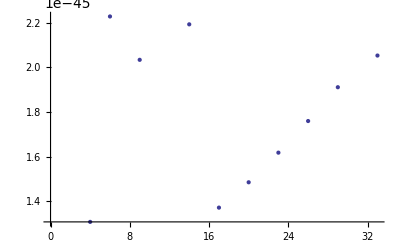

```mathematica
ListPlot[Fb22]
```

```mathematica
Fb2lx=Interpolation[Fb22,InterpolationOrder->5]
```

InterpolatingFunction[{{4.,33.}},<>]

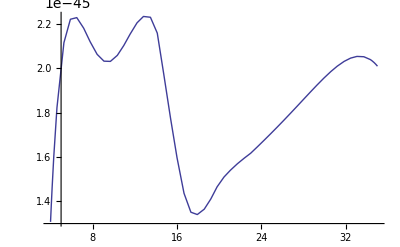

```mathematica
Plot[Fb2lx[m],{m,4,35}]
```

{{57.,1.7666×10^-45},{58.,6.2098×10^-46},{59.,1.8534×10^-52},{60.,2.9522×10^-52},{61.,4.7495×10^-53},{62.,2.0889×10^-51}}

{{57.,1.9456×10^-45},{58.,1.4877×10^-45},{59.,1.3935×10^-45},{60.,9.5461×10^-46},{61.,6.5902×10^-46},{62.,7.0707×10^-46}}

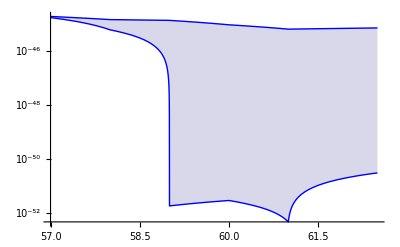

```mathematica
se2=(First[SortBy[#1,Last]]&)/@SplitBy[sigmpsinoncoh2[[All,{1,2}]],First]
se22=(Last[SortBy[#1,Last]]&)/@SplitBy[sigmpsinoncoh2[[All,{1,2}]],First]
fis2=Interpolation[se2[[All,{1,2}]],InterpolationOrder->1];
fis22=Interpolation[se22[[All,{1,2}]],InterpolationOrder->1];
figs1=Show[LogPlot[{fis2[m],fis22[m]},{m,57,62.5},PlotStyle->{Blue,Blue},Filling->{2->{1}}]]
```

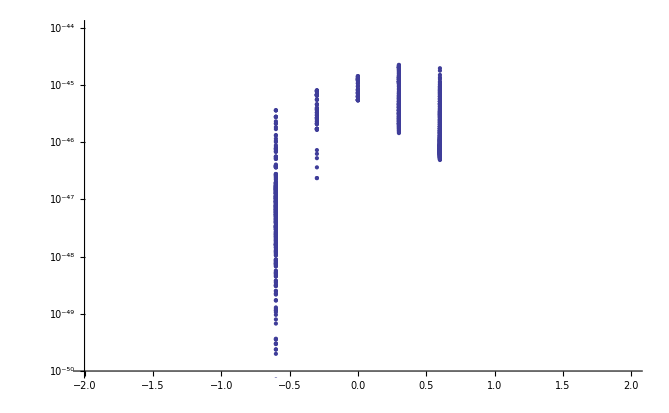

```mathematica
figlx=Show[ListLogPlot[{siglx},PlotRange->{{-2,2},{10^-50,10^-44}}]]
```

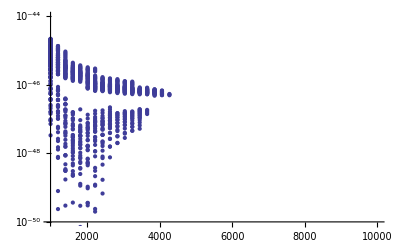

```mathematica
figlam=Show[ListLogPlot[{siglam},PlotRange->{{1000,10000},{10^-50,10^-44}}]]
```

InterpolatingFunction::dmval: Input value {591.081} lies outside the range of data in the interpolating function. Extrapolation will be used.

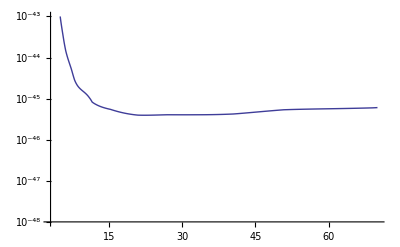

```mathematica
LogPlot[lux15[m],{m,3,70},PlotRange->{10.^-48,10.^-43}]
```

```mathematica
siglxvsmu=Table[{om[[i,1]],om[[i,5]]},{i,1,Length[om]}];
```

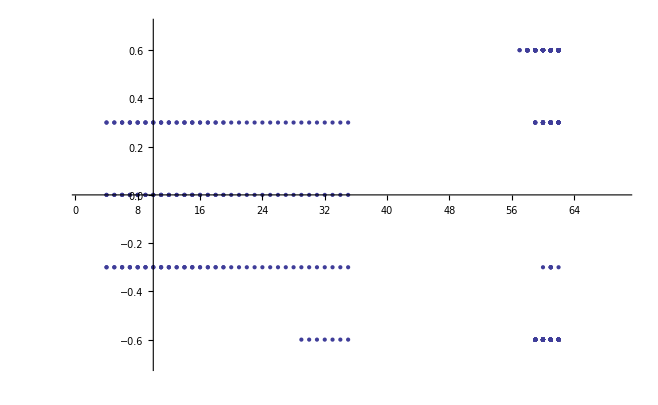

```mathematica
figlxvspars=Show[ListPlot[{siglxvsmu},PlotRange->{{1,70},{-.7,.7}}]]
```

```mathematica
tickSpecification=Table[{10^-(i),Superscript[10,-i]},{i,44,48}];
```

InterpolatingFunction::dmval: Input value {546.712} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {591.081} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {645.448} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

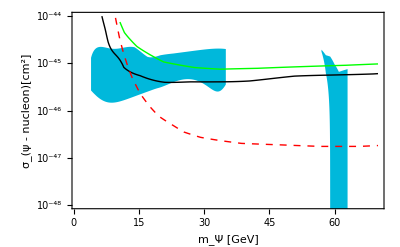

```mathematica
figsignocoh=Show[ListLogPlot[{sigmpsinoncoh},PlotRange->{{1,70},{10^-48,10^-44}},PlotStyle->Transparent,FrameTicks->Automatic],LogPlot[{Fb2lx[m],clx[m]},{m,4,35},PlotStyle->{None,None},Filling->{1->{2}},FillingStyle->RGBColor[0,0.72,0.86]],
LogPlot[{fis2[m],fis22[m]},{m,57,63},PlotStyle->{None,None},Filling->{2->{1}},FillingStyle->RGBColor[0,0.72,0.86]],
LogPlot[σlux[m],{m,4,70},PlotStyle->{Green},PlotLegends->Placed[LineLegend[{Green},{"Lux 90% C.L. (2014)"},LabelStyle->16],{0.58,.52}]],
LogPlot[lux15[m],{m,3,70},PlotStyle->{Black},PlotRange->{10^-48,10^-44},PlotLegends->Placed[LineLegend[{Black},{"Lux 90% C.L. (2015)"},LabelStyle->16],{0.58,.52}]],
LogPlot[xenon1t[m],{m,4,70},PlotStyle->{Red,Dashed},PlotLegends->Placed[LineLegend[{Red,Dashed},{"Xenon1T"},LabelStyle->16],{0.58,.52}]],
(*LogPlot[Atlas[m],{m,4,63.5},PlotRange->{10.^-48,10.^-43},PlotStyle->{Red, Dashed},Frame->{True,True,False,False},FrameLabel->{"\!\(\*SubscriptBox[\(m\), \(ψ\)]\) (GeV)","\!\(\*SubscriptBox[\(σ\), \(ψ - nucleon\)]\)(\!\(\*SuperscriptBox[\(cm\), \(2\)]\))"},PlotLegends->Placed[LineLegend[{Red},{"Atlas 90% C.L. (2015)"},LabelStyle->12],{0.655,.77}]]*)Frame->True,FrameLabel->{"m_Ψ [GeV]","\!\(\*SubscriptBox[\(σ\), \(ψ - nucleon\)]\)[\!\(\*SuperscriptBox[\(cm\), \(2\)]\)]"},LabelStyle->{(*FontWeight->"Bold"*)FontSize->20}(*ListLogLogPlot[t3,PlotRange->{{1,200},{0,2*10^10}},PlotStyle->{Blue}]*),PlotRangePadding->0,ImageSize->{GoldenRatio*400,400}]
```

```mathematica
Export["DDincoherent.pdf",figsignocoh]
```

DDincoherent.pdf

```mathematica
Export["DDcoherent.png",figsigcoh]
```

DDcoherent.png

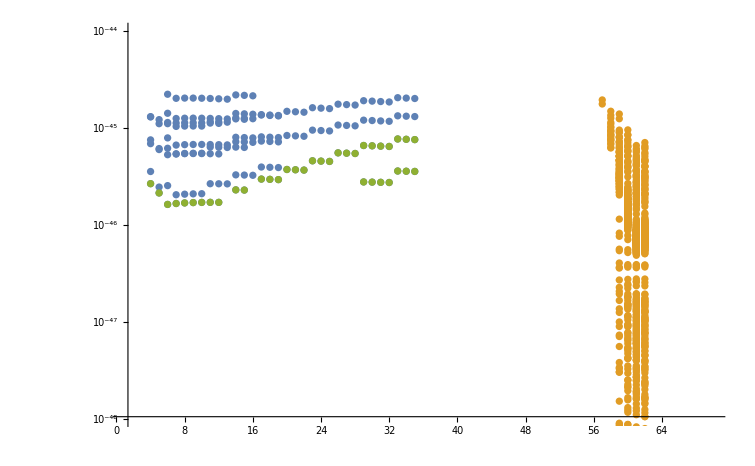

```mathematica
ListLogPlot[{sigmpsinoncoh,sigmpsinoncoh2,clx6},PlotRange->{{1,70},{10^-48,10^-44}}]
```

```mathematica
ListPlot3D[{sigmpsinoncoh3},PlotRange->{{1,28},{1000,1200},{0,2}}]
```

-Graphics3D-

List in order : Mpsi,  Lam,  mu (1), mu (3), Lx, kk, Om, SigmaPsiP, SigmaPsiN, SigTotIncoh, NuFlux from Sun, MuonFlux Upward, MuonFlux Contained, Z width, H width, HBR inv

Indirect Detection

```mathematica
vev=246.;
MH=125.7;
MZ=91.1876;
MW=80.401;
GZ=2.49;
GH=.004;
mτ=1.77682;
MTA=mτ;
mt=173.21;
MB=4.66;
(*cviiR=-10.;
cviiL=-8;*)
cw=MW/MZ;
gew=2*MW/vev;
gLmRb=-1+4/3 (cw^2-1);
gzz=gew/(4 Pi cw);
(*ciii=1.5;
cii=.1;*)
w=ArcCos[80.385/91.1876];
```

```mathematica
gevI2cm2=0.3894*10^(-27)2.9979*10^10;
```

```mathematica
svnn[mpsi_,mudm1_,mphi_,Lam_]:=gevI2cm2 2^4 mpsi^2 mudm1^4/(64 (mphi^2+mpsi^2)^2 Pi Lam^4 )
```

```mathematica
svnn2[mpsi_,etasq_,mphi_]:=gevI2cm2 2^4 mpsi^2 etasq^2/(64 (mphi^2+mpsi^2)^2 Pi )
```

```mathematica
Solve[svnn2[.1,x,(10+.1)*1]==3*10^-26,x]
```

{{x→-0.183335},{x→0.183335}}

```mathematica
Solve[svnn[1,.001*x^2,11,x]==3.*10^-26,x]
```

{{x→-148.067},{x→0.-148.067 ⅈ},{x→0.+148.067 ⅈ},{x→148.067}}

```mathematica
(gz^4 Sqrt[1-MB^2/mpsi^2] mpsi^2 Nf zi2di2^2 (1/4 (1+gLmGr^2+((-3+gLmGr^2) MB^2)/(2 mpsi^2)) Log[Λ/mphi]+(1/8 (1+gLmGr^2)+((-1+gLmGr^2) MB^2)/(16 mpsi^2)) (1+Log[Λ/mphi]^2)))/(64 (16 mpsi^4+Gz^2 MZ^2-8 mpsi^2 MZ^2+MZ^4) π )
```

(gz^4 √(1-21.7156/mpsi^2) mpsi^2 Nf zi2di2^2 (1/4 (1+gLmGr^2+(10.8578 (-3+gLmGr^2))/mpsi^2) Log[Λ/(10+mfe)]+(1/8 (1+gLmGr^2)+(1.35723 (-1+gLmGr^2))/mpsi^2) (1+Log[Λ/(10+mfe)]^2)))/(64 (6.9194×10^7-66521.4 mpsi^2+16 mpsi^4) π)

```mathematica
svffZ[mpsi_,Lam_,mu3_,mphi_,z_,MB_,gLmGr_,Nf_]:=gevI2cm2(gzz^4 Sqrt[1-MB^2/mpsi^2] mpsi^2 Nf (z*mu3/Lam)^4 (1/4 (1+gLmGr^2+((-3+gLmGr^2) MB^2)/(2 mpsi^2)) Log[Lam/mphi]+(1/8 (1+gLmGr^2)+(-1+gLmGr^2) MB^2 (1+Log[Lam/mphi]^2))/(8 mpsi^2)))/(64 (16 mpsi^4+GZ^2 MZ^2-8 mpsi^2 MZ^2+MZ^4) π)
```

```mathematica
svnn[mpsi,118,10+mpsi,1000]
```

(1.80107×10^-22 mpsi^2)/((mpsi^2+(10+mpsi)^2)^2)

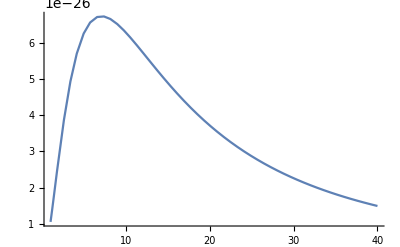

```mathematica
Plot[svnn[mpsi,114,10+mpsi,1000],{mpsi,1,40}]
```

InterpolatingFunction::dmval: Input value {620.378} lies outside the range of data in the interpolating function. Extrapolation will be used.

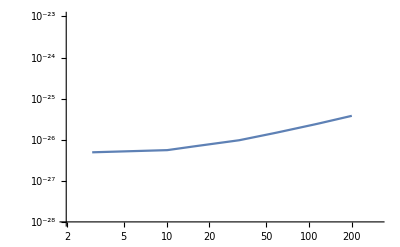

```mathematica
Get["/home/vanniagm/Dropbox/micromegas_3.6.9.2/DMSF2/fermilat.m"]
```

```mathematica
svbb[mpsi_,mudm3_,Lx_,Lam_,mphi_,z3_]:=(.001)^2*gevI2cm2(-3 (MB^2 (MB-mpsi) (MB+mpsi)Sqrt[1-MB^2/mpsi^2] (z3^2*mudm3^2+Lx vev^2 z3^2 Log[Lam/mphi])^2))/(256 ((GH^2 MH^2+(MH^2-4 mpsi^2)^2) Pi π^4 vev^4 Lam^2))
```

```mathematica
Listsvnn=Table[{om1[[i,1]],svnn[om1[[i,1]],om1[[i,3]],(10+om1[[i,1]])*om1[[i,6]],om1[[i,2]]]},{i,1,Length[om1]}];
Listsvnn2=Table[{om2[[i,1]],svnn[om2[[i,1]],om2[[i,3]],(10+om2[[i,1]])*om2[[i,6]],om2[[i,2]]]},{i,1,Length[om2]}];
```

```mathematica
Listsvff=Table[{om1[[i,1]],svffZ[om1[[i,1]],om1[[i,2]],om1[[i,4]],(10+om1[[i,1]])*om1[[i,6]],2,MB,gLmRb,3]},{i,1,Length[om1]}];
Listsvff2=Table[{om2[[i,1]],svffZ[om2[[i,1]],om2[[i,2]],om2[[i,4]],(10+om2[[i,1]])*om2[[i,6]],2,MB,gLmRb,3]},{i,1,Length[om2]}];
```

Check this results because sigmav was zero at first approx, it is missing a beta^2 factor, so it is expected to be lower.

```mathematica
Listsvbb=Table[{om[[i,1]],svbb[om[[i,1]],om[[i,4]],om[[i,5]],om[[i,2]],(10+om[[i,1]])*om[[i,6]],2]},{i,1,Length[om]}];
```

```mathematica
Lb1=(First[SortBy[#1,Last]]&)/@SplitBy[Listsvff[[All,{1,2}]],First];
Lb2=(Last[SortBy[#1,Last]]&)/@SplitBy[Listsvff[[All,{1,2}]],First];
Fb1=Interpolation[Lb1[[All,{1,2}]],InterpolationOrder->2];
Fb2=Interpolation[Lb2[[All,{1,2}]],InterpolationOrder->2];
```

{{57.,1.13564×10^-30},{58.,1.7421×10^-31},{59.,2.24193×10^-32},{60.,4.2887×10^-33},{61.,1.28181×10^-33},{62.,1.14233×10^-33}}

{{57.,1.31719×10^-30},{58.,1.10914×10^-30},{59.,1.15394×10^-30},{60.,1.13057×10^-30},{61.,5.4321×10^-31},{62.,4.8109×10^-31}}

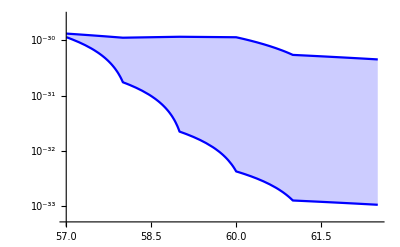

```mathematica
se2=(First[SortBy[#1,Last]]&)/@SplitBy[Listsvff2[[All,{1,2}]],First]
se22=(Last[SortBy[#1,Last]]&)/@SplitBy[Listsvff2[[All,{1,2}]],First]
fis2=Interpolation[se2[[All,{1,2}]],InterpolationOrder->1];
fis22=Interpolation[se22[[All,{1,2}]],InterpolationOrder->1];
figs1=Show[LogPlot[{fis2[m],fis22[m]},{m,57,62.5},PlotStyle->{Blue,Blue},Filling->{2->{1}}]]
```

InterpolatingFunction::dmval: Input value {686.725} lies outside the range of data in the interpolating function. Extrapolation will be used.

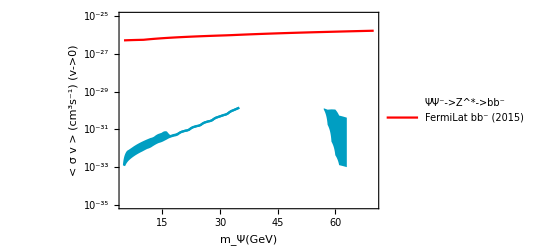

```mathematica
fsvbb=Show[ListLogPlot[{Listsvff(*,Listsvbb*)},PlotRange->{{5,70},{10^-35,10^-25}},PlotStyle->{Transparent},PlotLegends->Placed[PointLegend[{"ΨΨ^-->Z^*->bb^-"(*,"ΨΨ^-->H^*->bb^-"*)},LabelStyle->16,LegendFunction->"Frame",Background->White],{0.65,.49}]],
LogPlot[{Fb1[m],Fb2[m]},{m,4,35},PlotStyle->{RGBColor[0,0.62,0.76],RGBColor[0,0.62,0.76]},Filling->{1->{2}},FillingStyle->RGBColor[0,0.62,0.76]],LogPlot[{fis2[m],fis22[m]},{m,57,63},PlotStyle->{None,None},Filling->{2->{1}},FillingStyle->RGBColor[0,0.62,0.76]],LogPlot[Subscript[Φ,μ][m],{m,5,70},PlotStyle->{Red},PlotLegends->Placed[LineLegend[{Red},{"FermiLat bb^- (2015)"},LabelStyle->16],{0.65,.87}]],Frame->True,FrameLabel->{"m_Ψ(GeV)","< σ v > (\!\(\*SuperscriptBox[\(cm\), \(3\)]\)\!\(\*SuperscriptBox[\(s\), \(-1\)]\)) (v->0)"},LabelStyle->{(*FontWeight->"Bold"*)FontSize->20}(*ListLogLogPlot[t3,PlotRange->{{1,200},{0,2*10^10}},PlotStyle->{Blue}]*),PlotRangePadding->0,ImageSize->{GoldenRatio*400,400}]
```

```mathematica
Export["Fermilat.pdf",fsvbb]
```

Fermilat.pdf

InterpolatingFunction::dmval: Input value {464.989} lies outside the range of data in the interpolating function. Extrapolation will be used.

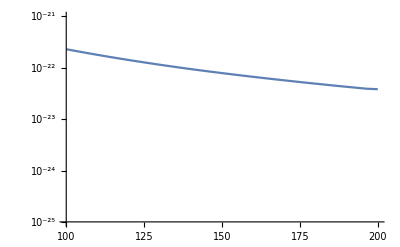

```mathematica
Get["/home/vanniagm/Dropbox/micromegas_3.6.9.2/DMSF2/icecube.m"]
```

```mathematica
Lb1=(First[SortBy[#1,Last]]&)/@SplitBy[Listsvnn[[All,{1,2}]],First];
Lb2=(Last[SortBy[#1,Last]]&)/@SplitBy[Listsvnn[[All,{1,2}]],First];
Fb1=Interpolation[Lb1[[All,{1,2}]],InterpolationOrder->2];
Fb2=Interpolation[Lb2[[All,{1,2}]],InterpolationOrder->2];
```

{{57.,6.36384×10^-27},{58.,6.50272×10^-28},{59.,4.97209×10^-29},{60.,4.6143×10^-30},{61.,8.92461×10^-31},{62.,1.21329×10^-30}}

{{57.,7.38017×10^-27},{58.,2.40917×10^-27},{59.,4.39714×10^-27},{60.,8.9742×10^-27},{61.,1.66732×10^-27},{62.,9.3953×10^-28}}

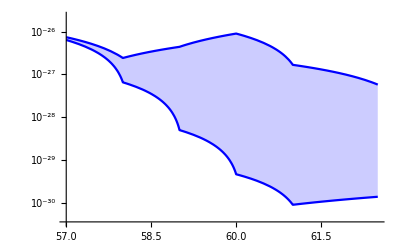

```mathematica
se2=(First[SortBy[#1,Last]]&)/@SplitBy[Listsvnn2[[All,{1,2}]],First]
se22=(Last[SortBy[#1,Last]]&)/@SplitBy[Listsvnn2[[All,{1,2}]],First]
fis2=Interpolation[se2[[All,{1,2}]],InterpolationOrder->1];
fis22=Interpolation[se22[[All,{1,2}]],InterpolationOrder->1];
figs1=Show[LogPlot[{fis2[m],fis22[m]},{m,57,62.5},PlotStyle->{Blue,Blue},Filling->{2->{1}}]]
```

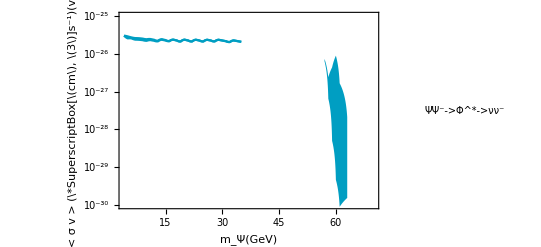

```mathematica
fsvnn=Show[ListLogPlot[Listsvnn,PlotRange->{{4,70},{10^-30,10^-25}},PlotStyle->{Transparent},PlotLegends->Placed[PointLegend[{"ΨΨ^-->Φ^*->νν^-"},LabelStyle->16,LegendFunction->"Frame",Background->White],{0.65,.49}]],LogPlot[{Fb1[m],Fb2[m]},{m,4,35},PlotStyle->{RGBColor[0,0.62,0.76],RGBColor[0,0.62,0.76]},Filling->{1->{2}},FillingStyle->RGBColor[0,0.62,0.76]],LogPlot[{fis2[m],fis22[m]},{m,57,63},PlotStyle->{None,None},Filling->{2->{1}},FillingStyle->RGBColor[0,0.62,0.76]],Frame->True,FrameLabel->{"m_Ψ(GeV)","< σ v > (\*SuperscriptBox[\(cm\), \(3\)]s^-1)(v->0)"},LabelStyle->{(*FontWeight->"Bold"*)FontSize->20}(*ListLogLogPlot[t3,PlotRange->{{1,200},{0,2*10^10}},PlotStyle->{Blue}]*),PlotRangePadding->0,ImageSize->{GoldenRatio*400,400}]
```

```mathematica
Export["SVnunu.pdf",fsvnn]
```

SVnunu.pdf

Neutrino Flux

```mathematica
km2yeartocm2s=1/(365*24*3600*10^10);
km3yeartocm3s=1/(365*24*3600*10^15);
```

```mathematica
listFluxnuCon=Table[{om1[[i,1]],om1[[i,13]]*km3yeartocm3s},{i,1,Length[om1]}];
listFluxnuCon2=Table[{om2[[i,1]],om2[[i,13]]*km3yeartocm3s},{i,1,Length[om2]}];
```

```mathematica
Lb1=(First[SortBy[#1,Last]]&)/@SplitBy[listFluxnuCon[[All,{1,2}]],First];
Lb2=(Last[SortBy[#1,Last]]&)/@SplitBy[listFluxnuCon[[All,{1,2}]],First];
Fb1=Interpolation[Lb1[[All,{1,2}]],InterpolationOrder->2];
Fb2=Interpolation[Lb2[[All,{1,2}]],InterpolationOrder->2];
```

{{57.,1.07135×10^-23},{58.,1.48288×10^-25},{59.,2.82528×10^-27},{60.,1.6042×10^-28},{61.,3.79059×10^-29},{62.,3.44527×10^-29}}

{{57.,1.81019×10^-23},{58.,8.58416×10^-24},{59.,6.95269×10^-23},{60.,1.57953×10^-22},{61.,2.16759×10^-24},{62.,1.2916×10^-24}}

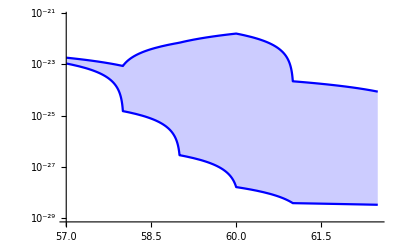

```mathematica
se2=(First[SortBy[#1,Last]]&)/@SplitBy[listFluxnuCon2[[All,{1,2}]],First]
se22=(Last[SortBy[#1,Last]]&)/@SplitBy[listFluxnuCon2[[All,{1,2}]],First]
fis2=Interpolation[se2[[All,{1,2}]],InterpolationOrder->1];
fis22=Interpolation[se22[[All,{1,2}]],InterpolationOrder->1];
figs1=Show[LogPlot[{fis2[m],fis22[m]},{m,57,62.5},PlotStyle->{Blue,Blue},Filling->{2->{1}}]]
```

```mathematica
listFluxnuUp=Table[{om1[[i,1]],om1[[i,12]]*km2yeartocm2s},{i,1,Length[om1]}];
listFluxnuUp2=Table[{om2[[i,1]],om2[[i,12]]*km2yeartocm2s},{i,1,Length[om2]}];
```

```mathematica
Lb1=(First[SortBy[#1,Last]]&)/@SplitBy[listFluxnuUp[[All,{1,2}]],First];
Lb2=(Last[SortBy[#1,Last]]&)/@SplitBy[listFluxnuUp[[All,{1,2}]],First];
Fb1=Interpolation[Lb1[[All,{1,2}]],InterpolationOrder->2];
Fb2=Interpolation[Lb2[[All,{1,2}]],InterpolationOrder->2];
```

{{57.,1.1061×10^-19},{58.,1.55296×10^-21},{59.,2.9921×10^-23},{60.,1.71455×10^-24},{61.,4.11847×10^-25},{62.,3.7963×10^-25}}

{{57.,1.86891×10^-19},{58.,8.98656×10^-20},{59.,7.38838×10^-19},{60.,1.7025×10^-18},{61.,2.36863×10^-20},{62.,1.42704×10^-20}}

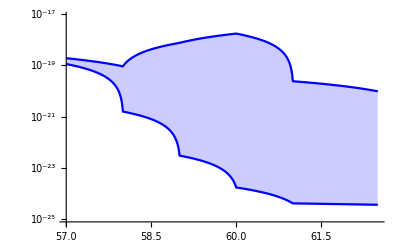

```mathematica
se2=(First[SortBy[#1,Last]]&)/@SplitBy[listFluxnuUp2[[All,{1,2}]],First]
se22=(Last[SortBy[#1,Last]]&)/@SplitBy[listFluxnuUp2[[All,{1,2}]],First]
fis2=Interpolation[se2[[All,{1,2}]],InterpolationOrder->1];
fis22=Interpolation[se22[[All,{1,2}]],InterpolationOrder->1];
figs1=Show[LogPlot[{fis2[m],fis22[m]},{m,57,62.5},PlotStyle->{Blue,Blue},Filling->{2->{1}}]]
```

```mathematica
Max[Table[om[[i,13]]*km2yeartocm2s,{i,1,Length[om]}]]
```

1.85325×10^-17

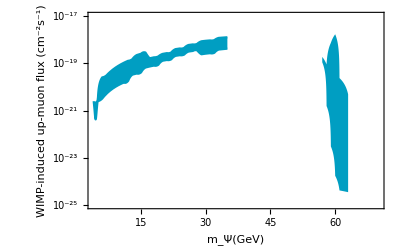

```mathematica
graphflux1=Show[ListLogPlot[{listFluxnuUp},PlotRange->{{4,70},{10^-25,10^-17}},PlotStyle->{Transparent}],
LogPlot[{Fb1[m],Fb2[m]},{m,4,35},PlotStyle->{RGBColor[0,0.62,0.76],RGBColor[0,0.62,0.76]},Filling->{1->{2}},FillingStyle->RGBColor[0,0.62,0.76]],
LogPlot[{fis2[m],fis22[m]},{m,57,63},PlotStyle->{None,None},Filling->{2->{1}},FillingStyle->RGBColor[0,0.62,0.76]],Frame->True,FrameLabel->{"m_Ψ(GeV)","WIMP-induced \n up-muon flux (\!\(\*SuperscriptBox[\(cm\), \(-2\)]\)\!\(\*SuperscriptBox[\(s\), \(-1\)]\))"},LabelStyle->{(*FontWeight->"Bold"*)FontSize->20}(*ListLogLogPlot[t3,PlotRange->{{1,200},{0,2*10^10}},PlotStyle->{Blue}]*),PlotRangePadding->0,ImageSize->{GoldenRatio*400,400}]
```

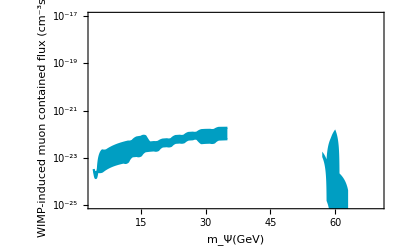

```mathematica
graphflux2=Show[ListLogPlot[{listFluxnuCon},PlotRange->{{4,70},{10^-25,10^-17}},PlotStyle->{Transparent}],LogPlot[{Fb1[m],Fb2[m]},{m,4,35},PlotStyle->{RGBColor[0,0.62,0.76],RGBColor[0,0.62,0.76]},Filling->{1->{2}},FillingStyle->RGBColor[0,0.62,0.76]],LogPlot[{fis2[m],fis22[m]},{m,57,63},PlotStyle->{None,None},Filling->{2->{1}},FillingStyle->RGBColor[0,0.62,0.76]],Frame->True,FrameLabel->{"m_Ψ(GeV)","WIMP-induced \n muon  contained flux (\!\(\*SuperscriptBox[\(cm\), \(-3\)]\)\!\(\*SuperscriptBox[\(s\), \(-1\)]\))"},LabelStyle->{(*FontWeight->"Bold"*)FontSize->20}(*ListLogLogPlot[t3,PlotRange->{{1,200},{0,2*10^10}},PlotStyle->{Blue}]*),PlotRangePadding->0,ImageSize->{GoldenRatio*400,400}]
```

```mathematica
Export["UpMuon.pdf",graphflux1]
```

UpMuon.pdf

```mathematica
Export["MuonCont.pdf",graphflux2]
```

MuonCont.pdf

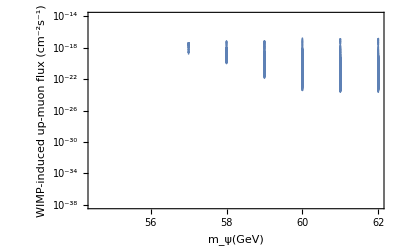

```mathematica
graphflux1=Show[ListLogPlot[Table[{om[[i,1]],om[[i,13]]*km2yeartocm2s},{i,1,Length[om]}],PlotRange->{10^-38,10^-14},Frame->{True,True,False,False},FrameLabel->{"\!\(\*SubscriptBox[\(m\), \(ψ\)]\)(GeV)","WIMP-induced \n up-muon flux (\!\(\*SuperscriptBox[\(cm\), \(-2\)]\)\!\(\*SuperscriptBox[\(s\), \(-1\)]\))"},LabelStyle->{FontWeight->"Bold",FontSize->18}],ImageSize->{GoldenRatio*500,500}]
```

Conversions

Ciii=Sqrt[2]*z3*mudm1/vev;
Cii=2*((Lam^2/vev^2)z3^2mudm3^2/Lam^2+Lx+z3^2*Log[Lam/mphi]);
CViiL=(Lam^2/vev^2)(z3^2 mudm3^2/Lam^2);
CViiR=(Lam^2/vev^2)(z3^2 mudm3^2/Lam^2)(Log[Lam/mphi]);

Higgs decay exluded region

```mathematica
om[[100]]
```

{4.,1000.,100.,13.1,0.3,1.,0.11304,1.1634×10^-46,9.6744×10^-47,1.0805×10^-46,1.7177×10^6,0.000023146,0.0030811,2.4068,0.0073165,0.1732}

```mathematica
Max[Table[(10+om[[i,1]])*om[[i,6]],{i,1,Length[om]}]]
```

288.

```mathematica
Max[Table[om[[i,6]],{i,1,Length[om]}]]
```

4.

```mathematica
vev=246;
```

```mathematica
RegHinv[Lam_,zz_,mu1_,mu3_,Lx_,ms_]:=(vev/Lam)Abs[(zz^2)((mu1^2+mu3^2)/vev^2+Lx*Log[Lam/ms])];
```

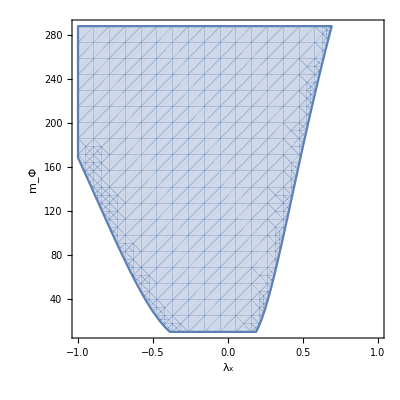

```mathematica
plot1=RegionPlot[RegHinv[1000,2,118,118,lx,ms]<1.3,{lx,-1,1},{ms,10,288},Frame->True,FrameLabel->{"λ_x","m_Φ",None,None}]
```

```mathematica
Export["plot1.pdf",plot1]
```

plot1.pdf

```mathematica
vev=246;
```

```mathematica
RegHinv[Lam_,zz_,mu1_,mu3_,Lx_,ms_]:=(vev/Lam)Abs[(zz^2)((mu1^2+mu3^2)/vev^2+Lx*Log[Lam/ms])];
```

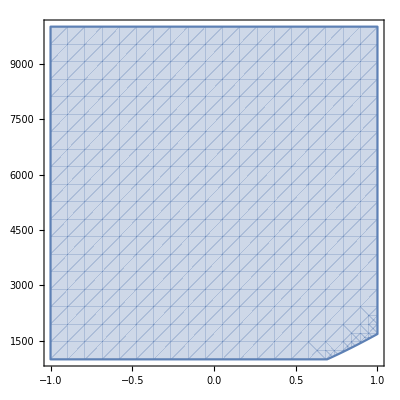

```mathematica
RegionPlot[RegHinv[Lam,2,118,118,lx,288]<1.3,{lx,-1,1},{Lam,1000,10000}]
```

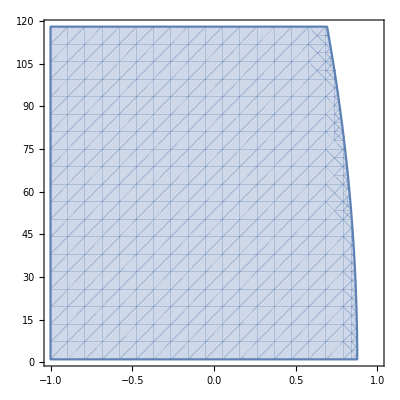

```mathematica
RegionPlot[RegHinv[1000,2,mu,118,lx,288]<1.3,{lx,-1,1},{mu,1,118}]
```

```mathematica
Sqrt[.0022/(125/(512*Pi^5))]
```

1.6606